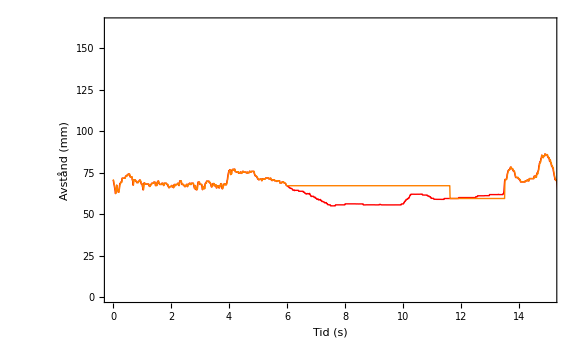
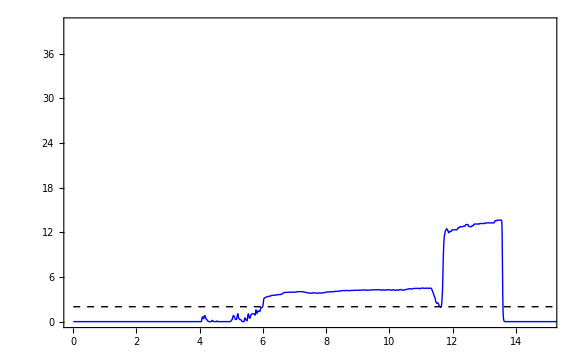

~/kandidat/Slutrapport/img/masterplot.pdf

```mathematica
ClearAll["Global`*"]
SetOptions[{Plot,ParametricPlot, ListLinePlot, ListPlot, LogLinearPlot},BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->11}];
apa =Import["~/masterapa2222", "Table"];
b = Transpose[apa];

data = {DataRange->{0, (Length[b[[1]]]-1)/100}
, ImagePadding->{{40, 40}, {40, 0}}, ImageSize->580};
xrange = {0, 15};

c1 = Blue;
c2 = Red;
force = ListLinePlot[b[[2]]
, PlotStyle -> c1
, Frame -> {False, False, False, True}
, FrameStyle->{Automatic,Automatic,Automatic, c1}
, PlotRange ->{xrange,{0, 40}}
, FrameLabel->{{None,Style["Trycksensor (N)", Bold]}, {None, None}}
, FrameTicks ->{Automatic, Automatic, Automatic,{2, 6, 10, 14}}
, data
, Epilog->{Dashed,Line[{{0,2},{100,2}}]}
];

p2 = ListLinePlot[{ b[[3]], b[[4]]}
, PlotStyle -> {c2, Orange}
, Frame -> {True, True, True, False}
, FrameStyle->{Automatic,c2,Automatic,Automatic}
, FrameLabel->{{Style["Avstånd  (mm)", Bold], None}, {"Tid (s)", None}}
, data
, PlotRange ->{xrange,{0, 165}}
];


final = Overlay[{p2, force}]
Export["~/kandidat/Slutrapport/img/masterplot.pdf", final]
```

```mathematica
|
```